## co prop 1.7W 3.4 vs 3.3 mW/mK 750 vs 970nm want the ULat to be much bigger than atom temp... ie 10uK. Ubkgrd<< bare tweezer depth

β^2=0.745447

w01=7.17644um

w02=7.17644um

zR1=208.769um

zR2=208.769um

frad=5.27505kHz (only makes sense if r1=0)

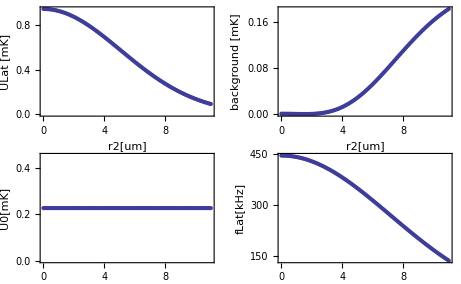

```mathematica
(*1=forw, 2=retro*)
Clear["Global`*"];
data=Reap[
Do[

cm=10^-2;
pm=10^-12;
nm=10^-9;
mW=10^-3;
um=10^-6;
mK=10^-3;
kHz=10^3;
amu=1.66054 10^-27;
a0=52.9177pm;
kB=1.38064852 10^-23;
m=132.90545 amu;
α=-1900;
c=299792458;

λ=775nm;
f2 = 50mm;
f1=16mm;

R =18mm/2;(*aperture of retro lens*)
R=R;(*just to account for clipping*)
w1=1.1mm/2;
w2=w1 f2/f1; (*waist of forward beam AT retro lens = waist of retro input beam*)
NA1=w1/f1;

NA2=Min[w2/f2,R/f2];
w01=λ/(π NA1); (*waist at focus of forw beam*)
w02=λ/(π NA2);
zR1=w01/NA1; 
zR2=w01/NA2;


wz1=w01 √(1+(z1/zR1)^2);
wz2=w02 √(1+(z2/zR2)^2);


(*Pretrofrac=1-ⅇ^(-(2 R^2)/w2^2);(*fraction of power of a beam of waist w transmitted thru an aperture of radius R*)
β=√Pretrofrac.5 ; (*ratio of retro E field to forw E field x some attenuation factor (experimental)*)
*)

Pforw=72.5mW; (*measured right before obj*)
Pretro = 54.7mW;(*measured right before retro*)

(*
Pin = 72.5mW;
β=√(Pretro/Pforw);*)
T3 = 1-(.2)/16.7; (*1- amount of power measured leaking through retro dichroic*)
β=√((Pforw (Pretro/Pforw)^(3/2)T3)/(√(Pretro Pforw)));(*modified to account for glass in the way.*)
Pin = √(Pforw Pretro); 

(*for retro reflected beam*)
sub={r1->3um, z1-> 50 um,z2->0zR2};(*radial and axial displacement. set to zero for perfect alignment*)
iLat=(8 Pin)/π(β Exp[-(r1^2/wz1^2+r2^2/wz2^2)])/(wz1 wz2)/.sub;
iforw=(2Pin)/π 1/wz1^2 Exp[-2 r1^2/wz1^2]/.sub;
ibkgrd=(√((2 Pin)/π)1/wz1 Exp[-r1^2/wz1^2]-β √((2 Pin)/π)1/wz2 Exp[-r2^2/wz2^2])^2/.sub; (*(Eforw-Eretro)^2*)

ULat=-1/(2ϵ0 c)(4 π ϵ0 α a0^3) iLat;
U0=-1/(2ϵ0 c)(4 π ϵ0 α a0^3) iforw;(*for foward beam only*)
Ubkgrd=-1/(2ϵ0 c)(4 π ϵ0 α a0^3) ibkgrd;

(*
U0=kB 0.6mK  (Pin/(3 mW))3.3/2.7(800nm/w01)^2; (*bare lattice beam (no retro)*)
ULat=4U0 NA2/NA1 β;
d=2U0 NA2/NA1 β Cos[(4 π z)/λ]; (*functional form of lattice potential*)
Ubkgrd=U0(1-NA2/NA1 β)^2;
*)

d=ULat/2 Cos[(4 π z)/λ]; (*functional form of lattice potential*)
a=Normal[Series[d,{z,0,2}]]; (*harmonic approx*)

(*bare forward lattice beam only*)
frad=√(Abs[U0]/(m (π  w01)^2));(*only makes sense for perfect alignment. *)
fax=(λ frad)/(√2 π w01);

fLat=fLat0/.Solve[-1/2 m(2π fLat0)^2== Coefficient[a,z^2],fLat0][[2]]; (*lattice freqs*)
xAxisStr="r2[um]";
Sow[{r2/um,ULat/kB/mK,Ubkgrd/kB/mK,U0/kB/mK,fLat/kHz,frad/kHz}]
,{r2,0,11um,.1um}]
][[2,1]];
"β^2="<>ToString[β^2]
"w01="<>ToString[w01/um]<>"um"
"w02="<>ToString[w02/um]<>"um"
"zR1="<>ToString[zR1/um]<>"um"
"zR2="<>ToString[zR2/um]<>"um"
"frad="<>ToString[frad/kHz]<>"kHz (only makes sense if r1=0)"
GraphicsGrid[{
{
ListPlot[data[[All,{1,2}]],Axes->False,Frame->True,FrameLabel->{xAxisStr,"ULat [mK]"}],
ListPlot[data[[All,{1,3}]],Axes->False,Frame->True,FrameLabel->{xAxisStr,"background [mK]"}]},
{
ListPlot[data[[All,{1,4}]],Axes->False,Frame->True,FrameLabel->{xAxisStr,"U0[mK]"}],
ListPlot[data[[All,{1,5}]],Axes->False,Frame->True,FrameLabel->{xAxisStr,"fLat[kHz]"}]
}
}
]
```

## check scattering rate for forward beam ONLY

```mathematica
MHz=10^6;
s=Pin/(π w01^2)/(2.7 mW/cm^2);
Γ =32 MHz;
Δ = 2π 3. 10^8(852-780)/852^2 1/nm;
Γ/2 s/(1+s+((2 Δ)/Γ)^2)
```

1.6892

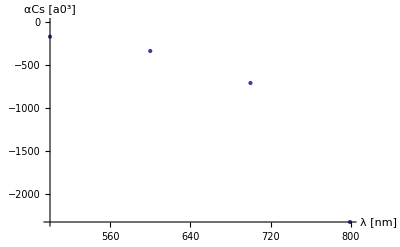

```mathematica
ListPlot[Thread[{{500,600,700,799.3},{-166.3,-333.9,-707.9,-2333}}],AxesLabel->{"λ [nm]","αCs [a0^3]"}]
```

## measured divergence of lattice beam

```mathematica
Clear["Global`*"];
FullSimplify[(1/w1 Exp[-r1^2/w1^2]+β 1/w2 Exp[-r2^2/w2^2])^2-(1/w1 Exp[-r1^2/w1^2]-β 1/w2 Exp[-r2^2/w2^2])^2]
```

(4 ⅇ^(-r1^2/w1^2-r2^2/w2^2) β)/(w1 w2)

{aa→0.000894775,bb→0.00109773}

{aa→0.00054283,bb→0.00110629}

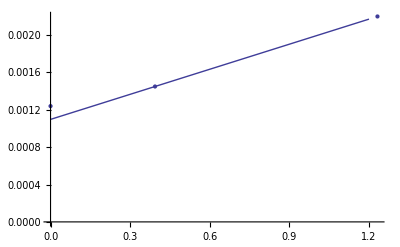

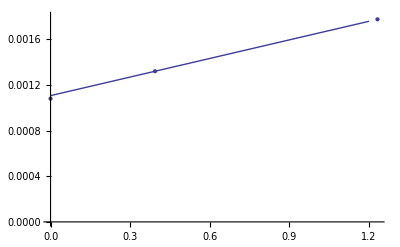

```mathematica
in=0.0254;
um=10^-6;

div=Thread[{{0,15.5,48.5}in,{1240,1450,2200}um,{1080,1320,1775}um}];
dat1=div[[;;,{1,2}]];
dat2=div[[;;,{1,3}]];

fitfn=aa z +bb;
fit1= FindFit[dat1[[2;;]],fitfn,{aa,bb},z]
fit2= FindFit[dat2[[2;;]],fitfn,{aa,bb},z]


Show[{ListPlot[dat1,PlotRange->{All,{0,.0022}}],Plot[fitfn/.fit1,{z,0,1.2}]}]
Show[{ListPlot[dat2,PlotRange->{All,{0,.0018}}],Plot[fitfn/.fit2,{z,0,1.2}]}]
```

```mathematica
ArcTan[aa]/10^-3/.fit1
ArcTan[aa]/10^-3/.fit2
```

0.894774

0.54283

```mathematica
2ArcTan[(#[[3,2]]-#[[2,2]])/(2 (#[[3,1]]-#[[3,2]]))]/10^-3&@dat2
```

0.369881

```mathematica
#
```

#1

```mathematica
1. (775nm)/(π 1000um)/10^-3
```

2.4669×10^8 nm

## derive expression for the bkgd on blue lattice:

```mathematica
Clear["Global`*"]
```

```mathematica
FullSimplify[(√((2 Pin)/π)1/w1z Exp[-r1^2/w1z^2]-β √((2 Pin)/π)1/w2z Exp[-r2^2/w2z^2])^2]
```

(2 ⅇ^(-(2 r1^2)/w1z^2-(2 r2^2)/w2z^2) Pin (ⅇ^(r2^2/w2z^2) w2z-ⅇ^(r1^2/w1z^2) w1z β)^2)/(π w1z^2 w2z^2)